```mathematica
<<NDSolve`FEM`
ex1={0,2Pi,.5Cos[2u]-.5,.8+ .5Sin[u]};
ex2={0,2,0,1};

(* Mathematical utils *)
div[U_]:=D[U[[1]],x]+D[U[[2]],y];
grad[f_]:={D[f,x],D[f,y]};

(* Channel construction *)
createChannel[y1_,y2_]:=Module[{p,U},
p={u,y1+v(y2-y1)};
U=Simplify[D[p,u]/.v->((y-y1)/(y2-y1))/.u->x];
{p,U}
];


harmonicData[ch_]:=Module[{sz},
sz=10;
meshOut=ToElementMesh[ch,{{-sz,sz},{-sz,sz}},MaxCellMeasure->.001,"MeshOrder"->1];
fOut=NDSolveValue[{∇_{x,y}^2 ψ[x,y] ==0,
DirichletCondition[ψ[x, y] == 0.0, x==uMin],
DirichletCondition[ψ[x, y] == 1.0, x==uMax]}, ψ, {x, y} ∈ meshOut];
gfOut=grad[fOut[x,y]];
{meshOut,fOut,gfOut}
];

getLevelSets[ϕ_,domain_,lMin_,lMax_,lInc_]:=Module[{ls,solG},
ls=Table[c,{c,lMin,lMax,lInc}];
solG=ContourPlot[ϕ[x,y],{x,y}∈domain,Contours->ls,AspectRatio->Automatic,ContourShading->None,
PerformanceGoal->"Quality",
PlotPoints->100];
{ls,Reverse[Cases[Normal@solG,Line[x_]:>x,Infinity]]}
];
```

# Finding harmonic coordinates

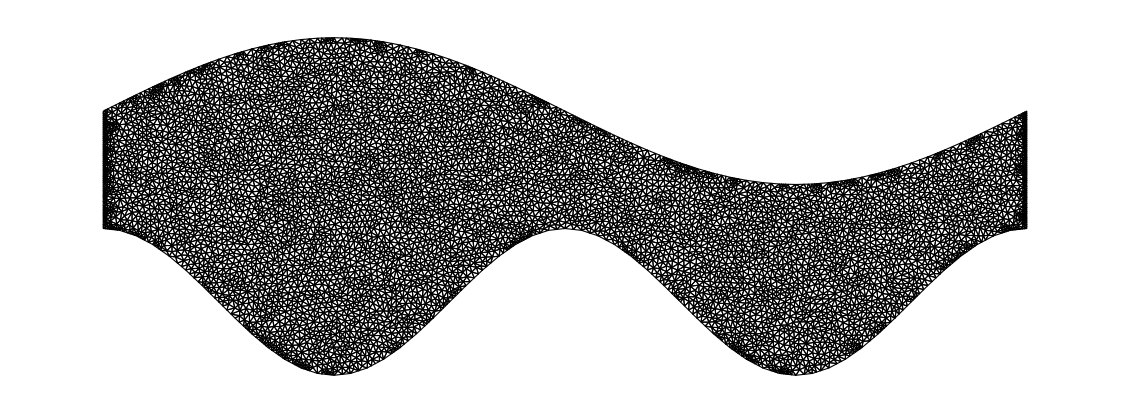

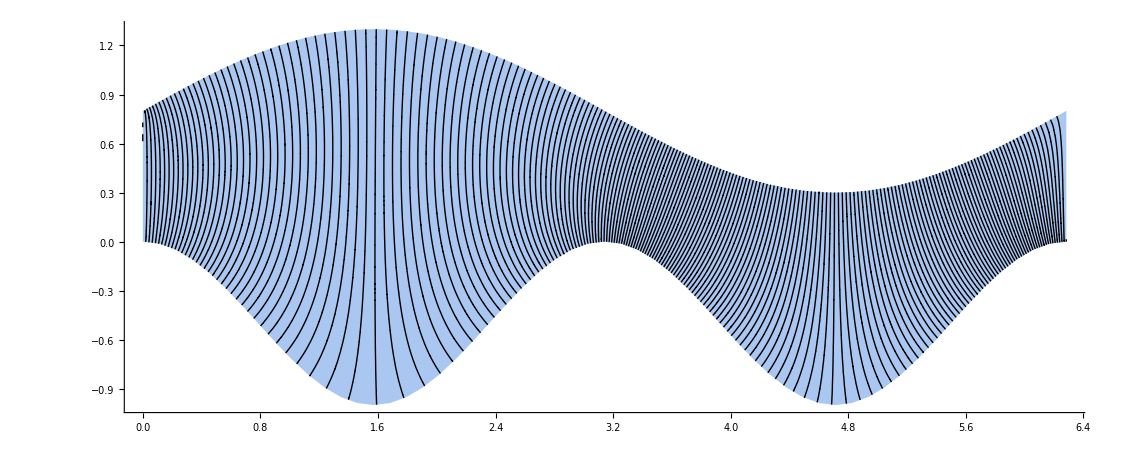

```mathematica
{uMin,uMax,y1,y2}=ex1;
{p,U}=createChannel[y1,y2];
ch=ParametricRegion[p,{{u,uMin,uMax},{v,0,1}}];

{mesh,ϕ,gϕ}=harmonicData[ch];
mesh["Wireframe"]

{levels,levelSets}=getLevelSets[ϕ,mesh,0,1,.005];
lG=ListPlot[levelSets,Joined->True,PlotStyle->Directive[Black,Thin]];
Show[Region[ch],lG,Axes->True]
```

# Computing effective diffusion coefficient

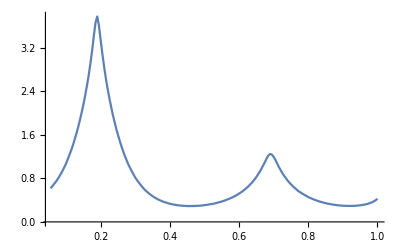

```mathematica
dc[l_]:=Module[{p,xm,ym,dp,dx,dy,Ux,Uy,USq,cJ},
(* Compute this!!! *)
cJ=.1;
(* Computing level edges centers *)
p = MovingAverage[levelSets[[l]],2];
{xm,ym}=Transpose[p];
(* Computing level edges increments *)
dp = Differences[levelSets[[l]]];
{dx,dy}=Transpose[dp];
(* Computing field at level edges centers *)
{Ux,Uy}=gϕ/.{x->xm,y->ym};
USq=Ux^2+Uy^2;
Ux=Ux/USq;
Uy=Uy/USq;
(* Integrating form at level *)
cJ Abs[Total[Uy dx-Ux dy]]
];

(* Plot results *)

ListPlot[Table[{levels[[i]], dc[i]},{i,12,Length[levels]}],PlotRange->Full,Joined->True]
(* ListPlot[{xm,ym}] *)
```